```mathematica
(*H1x*)
SetDirectory["/Users/aditya/Downloads/vortex"]
m = 0.50; 
lam = 1;(* next nearest neighbour hopping (diagonal)*)
t[0][0] = 3/2*m;
t[-1][0] = -m;
t[0][-1] = -m;
t[1][0] = -m;
t[0][1] = -m;
t[-1][-1] = m/4;
t[1][-1] = m/4;
t[-1][1] = m/4;
t[1][1] = m/4;
(*SOC spinorbit*)
l[-1][0] = lam(1-I);
l[0][-1] = lam(1-I);
l[1][0] = lam(1-I);
l[0][1] = lam(1-I);
Nx = 28;
Ny = 28;
i = 0;

For[ix = 1, ix <= Nx, ix++,
 For[iy = 1, iy <= Ny, iy++, i++;
  xpos[i] = ix;
  ypos[i] = iy;]]
NN = i;

Vimp = 0;
empty= SparseArray[{x_, y_} -> 0, {NN, NN}];
(*Hopping Matrix*)
tijmn = Table[
   If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)],
    If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])],
     If[NumericQ[t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)],
      If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)],
       If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])],
        If[NumericQ[t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)],
         If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)],
          If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])],
           If[NumericQ[t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]], t[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]]]]]]]]]],
   {i, 1, NN}, {j, 1, NN}];
For[i = 1, i <= NN, i++,
  For[j = 1, j <= NN, j++,
   tij[i][j] = tijmn[[j, i]]
   ]];
Clear[tijmn]
H1= SparseArray[{x_, y_} /; NumericQ[tij[x][y]] -> tij[x][y], {NN, NN}];
tijmn = Table[
   If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] - Ny)],
    If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j])],
     If[NumericQ[l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j] - Nx)][ypos[i] - (ypos[j] + Ny)],
      If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] - Ny)],
       If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j])],
        If[NumericQ[l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j])][ypos[i] - (ypos[j] + Ny)],
         If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] - Ny)],
          If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j])],
           If[NumericQ[l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]], l[xpos[i] - (xpos[j] + Nx)][ypos[i] - (ypos[j] + Ny)]]]]]]]]]],
   {i, 1, NN}, {j, 1, NN}];
For[i = 1, i <= NN, i++,
  For[j = 1, j <= NN, j++,
   tij[i][j] = tijmn[[j, i]]
   ]];
Clear[tijmn]
soc= SparseArray[{x_, y_} /; NumericQ[tij[x][y]] -> tij[x][y], {NN, NN}];
Clear[mu]
Chempot1[mu_]:= SparseArray[{x_, x_} ->  -mu, {NN, NN}];
(*Chempot2[mu_]:= SparseArray[{y_, y_} ->  -mu, {NN, NN}];*)
(*Chempot[mu]=ArrayFlatten[{{Chempot1[mu], empty}, {empty,Chempot1[mu]}}];*)
Hop1x[mu_]:= ArrayFlatten[{{H1-Chempot1[mu],soc}, {ConjugateTranspose[soc], -H1-Chempot1[mu]}}];(*adding pauli matrix σx*)
(*HermitianMatrixQ[Hop1x[0]];
MatrixForm[Hop1x[]];*)
```

/Users/aditya/Downloads/vortex

```mathematica
(*------onsite------*)
Clear[s,st,stab,sij,SCs,dmn,dmm]

js={};
For[i=1,i<=NN,i++,jisel={};
For[j=1,j<=NN,j++,
If[xpos[i]==xpos[j],
If[ypos[i]==ypos[j],AppendTo[jisel,j]]]];AppendTo[js,jisel]]



SCs1=SparseArray[{x_,y_}/;Not[TrueQ[sij[x][y]==Null]]->0,{NN,NN}];
SCs2[st_]:= SparseArray[{Band[{1,1}]-> Flatten[st]}, {NN, NN}];
SCs3=SparseArray[{x_,y_}/;Not[TrueQ[sij[x][y]==Null]]->0,{NN,NN}];
SCs[st_]:= ArrayFlatten[{{SCs1, SCs2[st]}, {SCs2[st], SCs1}}];
Clear[sij]
s[i_,j_]:=Take[st[[i,j]]];
```

```mathematica
f[x_]:=1./(Exp[x/kT]+1.);
kT = 0.001 (*eV*);
f[x_] :=(*UnitStep[x]*)(*1./(Exp[x/kT]+1.);*)If[Re[x] > 0.02, 0.0,
   If[Re[x] < -0.02, 1.0,
    1./(Exp[Re[x]/kT] + 1.)]];

(*mtuss={};*)
(*For[k=0,k≤0.2,k=k+0.1,
Print[StringJoin["calculte..",ToString[k]]];*)
(*flag1 = 1;*)
(*m = 0.5*0;*)
(*Us = 0.0;*)
vs = -1.25;(*s-wave pairing interaction*)
(*vd = -0.2*0; d-wave pairing interaction*)
mu = 0;

nexp = 1; (*expected electro density in your system*)
(*ntot = 1;
nut=Table[(ntot/2.)+((m*(-1)^(xpos[i]+ypos[i]))/2),{i,1,NN}];
ndt=Table[(ntot/2.)-((m*(-1)^(xpos[i]+ypos[i]))/2),{i,1,NN}];*)

Clear[v,as,b,bm];

(*dsignn={}; (*initialisation of d-wave sign*)
For[i=1,i<=NN,i++,jisel={};
For[j=1,j<=NN,j++,
If[xpos[i]==xpos[j],
If[ypos[i]==ypos[j]+1,AppendTo[jisel,-1],
If[ypos[i]==ypos[j]-1,AppendTo[jisel,-1],
If[ypos[i]==ypos[j]+(Ny-1),AppendTo[jisel,-1],
If[ypos[i]==ypos[j]-(Ny-1),AppendTo[jisel,-1]]]]],
If[ypos[i]==ypos[j],
If[xpos[i]==xpos[j]+1,AppendTo[jisel,1],
If[xpos[i]==xpos[j]-1,AppendTo[jisel,1],
If[xpos[i]==xpos[j]+(Nx-1),AppendTo[jisel,1],
If[xpos[i]==xpos[j]-(Nx-1),AppendTo[jisel,1]]]]]]]];
AppendTo[dsignn,jisel]];
spmtnn=Table[dsignn[[i,j]]*dijnn,{i,1,NN},{j,1,4}];
dijnn=0.3;*)

st=Table[ds,{i,1,NN},{j,1}]; (*initialisation of s-wave*)
ds=-0.01; (*Gap size*)
(*AbsoluteTiming[*)
(*MatrixForm[SCs[st]]*)
```

```mathematica
(*
 Huu = Ho (*+imp*)(**+Hartree*);
  Hvv = -ConjugateTranspose[Ho (*-imp*)(*+Hartree2*)];
  Huv= SCs[st]; (*Superconducting part Δ*)
  Hvu=ConjugateTranspose[Huv];
  H = ArrayFlatten[{{Huu, Huv}, {Hvu, Hvv}}]; 
MatrixForm[H];*)
```

```mathematica
(*calculation mean fields via iteration*)(*Main Hamiltonian BDG*)
iter = 100;
  (*em =  SparseArray[{x_, x_} -> 0, {NN, NN}];*)
For[a = 1, a <= iter, a++,
  (*mtus={};*)
  Huu = H1-Chempot1[mu] (*+imp*)(**+Hartree*);
  Hdd = H1-Chempot1[mu];
Hud = soc;
Hdu = Conjugate[soc];
hh1 = ArrayFlatten[{{Huu,Hud}, {Hdu, Hdd}}];
hh2 = ArrayFlatten[{{-Conjugate[Huu],Conjugate[Hud]}, {Conjugate[Hdu], -Conjugate[Hdd]}}];
    Huv= SCs[st]; (*Superconducting part Δ*)
  Hvu=Conjugate[Huv];
  H = ArrayFlatten[{{hh1, Huv}, {Hvu, hh2}}]; (*Joins all the matrices*)
 (* Print[HermitianMatrixQ[H]];*)
  (*Print[MatrixForm[H]];*)
  
  ES = Eigensystem[H];
 
  fermi = Map[f, ES[[1]]];
  (*tab = Table[1,{i,Length[fermi]}];*)
  nutcalc = Table[((Abs[ES[[2]][[;; , i]]])^2.) . fermi, {i, 1, NN}];
  
  
  ndtcalc = Table[((Abs[ES[[2]][[;; , i + 3NN]]])^2.) . (1. - fermi), {i, 1, NN}];
  
  
  ni = nutcalc + ndtcalc;
  mi = nutcalc - ndtcalc;
  nt = Total[ni]/NN;
  mt = Total[Abs[mi]]/NN;
  
vsite = 378;
  l=0.3;(*penetration depth*)
  zetanot=l/Pi;(*coherence length*)
    stcalc=Table[
  If[xpos[i]==xpos[vsite],
  phi=Pi/2,
  phi=ArcTan[(Abs[ypos[i]-ypos[vsite]])/(Abs[xpos[i]-xpos[vsite]])];
  ];
  vs*((Inner[Times,ES[[2]][[;;,i]],Conjugate[ES[[2]][[;;,j+
  3NN]]],List])+(Inner[Times,ES[[2]][[;;,i+NN]],Conjugate[ES[[2]][[;;,i+
  2NN]]],List])).fermi*
  Tanh[Sqrt[(xpos[i]-xpos[vsite])^2+(ypos[i]-ypos[vsite])^2]/zetanot]*
  Exp[I*phi]
,{i,1,NN},{j,js[[i]]}];
  (*Print["till here"];*)
  

  (*spmtcalcnn=Table[vd*((Inner[Times,ES[[2]][[;;,i]],ES[[2]][[;;,j+
  NN]],List])+(Inner[Times,ES[[2]][[;;,j]],ES[[2]][[;;,i+
  NN]],List])).fermi,{i,1,NN},{j,jspmnn[[i]]}];*)
  
  
  sta=Total[Flatten[stcalc]]/NN;(*
  stann=Total[Total[Abs[spmtcalcnn]]]/NN*0.25;*)
  
  
  
  Print[a , " mu=", mu, "  mt=", mt,(*" Us=", Us,*)"  n=", nt ,"  sup=", Abs[ sta(*"  supnn=",  stann*)]];
  mu = mu - 0.1*(nexp - nt);
  (*nut=0.5*nutcalc+0.5*nut;
  ndt=0.5*ndtcalc+0.5*ndt;*)
  st=0.5*stcalc+0.5*st;
  (*spmtnn=0.5*spmtcalcnn+0.5*spmtnn;*)
  ];
(*AppendTo[mtuss,{vd,stann}];
];*)


Export["Huu.wdx",Huu];
Export["Hud.wdx",Hud];
Export["Hdu.wdx",Hdu];
Export["Hdd.wdx",Hdd];
Export["SCs.wdx",SCs[st]];
```

1 mu=0  mt=6.11756×10^-16  n=0.834232  sup=1/784 Abs[(-0.00454796+1.48598×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.48598×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.43693×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.43693×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.74667×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.74667×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.88287×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.88287×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.68329×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.68329×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.30016×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.30016×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.29362×10^-19 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.29362×10^-19+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.06202×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.06202×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.33116×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.33116×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.64576×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.64576×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.85769×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.85769×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.91638×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.91638×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.04163×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.04163×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.07118×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.07118×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.18337×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.18337×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.6674×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.6674×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.76524×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.76524×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.79481×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.79481×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.94084×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.94084×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.36973×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.36973×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.56258×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.56258×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.69923×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.69923×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.74537×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.74537×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.98727×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.98727×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.11579×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.11579×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.12214×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.12214×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.62588×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.62588×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.63316×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.63316×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.33579×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.33579×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.84917×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.84917×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.15047×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.15047×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.35771×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.35771×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.75761×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.75761×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.76579×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.76579×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.89876×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.89876×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.90955×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.90955×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.93992×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.93992×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.00705×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.00705×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.1274×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.1274×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.36492×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.36492×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.27202×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.27202×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.31083×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.31083×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.35958×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.35958×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.76127×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.76127×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.77496×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.77496×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.77987×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.77987×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.78578×10^-18 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.78578×10^-18+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.02081×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.02081×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.03743×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.03743×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.04959×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.04959×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.05277×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.05277×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.06321×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.06321×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.07904×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.07904×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.09621×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.09621×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.12812×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.12812×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.14881×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.14881×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.19508×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.19508×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.20262×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.20262×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.22323×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.22323×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.24867×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.24867×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.25625×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.25625×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.2697×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.2697×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.3044×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.3044×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.33058×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.33058×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.34596×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.34596×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.38616×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.38616×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.40206×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.40206×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.40685×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.40685×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.4087×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.4087×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.418×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.418×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.46832×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.46832×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.47662×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.47662×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.49229×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.49229×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.51249×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.51249×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.51569×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.51569×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.51803×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.51803×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.56988×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.56988×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.67468×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.67468×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.75778×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.75778×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.77024×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.77024×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.79848×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.79848×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.92321×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.92321×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.92485×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.92485×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.97557×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.97557×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.98963×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.98963×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.00482×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.00482×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.03358×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.03358×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.16522×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.16522×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.16544×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.16544×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.22755×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.22755×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.23903×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.23903×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.24365×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.24365×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.24476×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.24476×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.28043×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.28043×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.35467×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.35467×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.35633×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.35633×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.36604×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.36604×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.40247×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.40247×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.43821×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.43821×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.4728×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.4728×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.49578×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.49578×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.52808×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.52808×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.57164×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.57164×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.62951×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.62951×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.67468×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.67468×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.67602×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.67602×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.68116×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.68116×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.69578×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.69578×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.72857×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.72857×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.74776×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.74776×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.78703×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.78703×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.81838×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.81838×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.82428×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.82428×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.82853×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.82853×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.94341×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.94341×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.99589×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.99589×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.11595×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.11595×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.13355×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.13355×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.14118×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.14118×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.17028×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.17028×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.1872×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.1872×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.21355×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.21355×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.22699×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.22699×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.30894×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.30894×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.32144×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.32144×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.44072×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.44072×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.46918×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.46918×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.50871×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.50871×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.51688×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.51688×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.53411×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.53411×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.60618×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.60618×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.61875×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.61875×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.62558×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.62558×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.64142×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.64142×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.65685×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.65685×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.67404×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.67404×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.71682×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.71682×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.77346×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.77346×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.78019×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.78019×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.81967×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.81967×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.84601×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.84601×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.88242×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.88242×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.89035×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.89035×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.90489×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.90489×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.94426×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.94426×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-3.97946×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((3.97946×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.01086×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.01086×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.02594×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.02594×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.07645×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.07645×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.10166×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.10166×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.14477×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.14477×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.16609×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.16609×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.1968×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.1968×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.25276×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.25276×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.27469×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.27469×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.34438×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.34438×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.50379×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.50379×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.52812×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.52812×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.55045×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.55045×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.55661×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.55661×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.56136×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.56136×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.6112×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.6112×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.61554×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.61554×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.61823×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.61823×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.62264×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.62264×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.66621×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.66621×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.67808×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.67808×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.71039×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.71039×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.72602×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.72602×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.75143×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.75143×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.77992×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.77992×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.80379×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.80379×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.80776×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.80776×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.82917×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.82917×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.89667×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.89667×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.90687×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.90687×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.91771×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.91771×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.93891×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.93891×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.95584×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.95584×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-4.97729×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((4.97729×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.11587×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.11587×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.1214×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.1214×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.19041×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.19041×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.20804×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.20804×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.22376×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.22376×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.22489×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.22489×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.25805×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.25805×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.27656×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.27656×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.29986×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.29986×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.34017×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.34017×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.34186×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.34186×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.34333×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.34333×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.35205×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.35205×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.36444×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.36444×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.37238×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.37238×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.38493×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.38493×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.42066×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.42066×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.45116×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.45116×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.46691×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.46691×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.46885×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.46885×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.4779×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.4779×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.49595×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.49595×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.56023×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.56023×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.57146×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.57146×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.57597×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.57597×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.59408×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.59408×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.59883×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.59883×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.70165×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.70165×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.78736×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.78736×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.86508×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.86508×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.86864×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.86864×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.87262×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.87262×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.89196×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.89196×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.89287×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.89287×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.95538×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.95538×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.96863×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.96863×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-5.99398×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((5.99398×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.04118×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.04118×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.07251×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.07251×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.15364×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.15364×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.17308×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.17308×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.20672×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.20672×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.21387×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.21387×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.22222×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.22222×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.25996×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.25996×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.27459×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.27459×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.28303×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.28303×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.28748×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.28748×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.30497×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.30497×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.32373×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.32373×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.36972×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.36972×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.40832×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.40832×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.41385×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.41385×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.41711×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.41711×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.42707×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.42707×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.44699×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.44699×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.47035×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.47035×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.52899×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.52899×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.5418×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.5418×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.55986×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.55986×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.60531×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.60531×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.68657×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.68657×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.74295×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.74295×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.77309×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.77309×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.78679×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.78679×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.86926×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.86926×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.87379×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.87379×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.89596×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.89596×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.90537×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.90537×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.9534×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.9534×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.99797×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.99797×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-6.99978×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((6.99978×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.04889×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.04889×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.10536×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.10536×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.17604×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.17604×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.18772×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.18772×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.21862×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.21862×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.24386×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.24386×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.24589×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.24589×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.28894×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.28894×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.32×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.32×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.35444×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.35444×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.41017×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.41017×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.53855×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.53855×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.54703×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.54703×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.55837×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.55837×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.63456×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.63456×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.68857×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.68857×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.70113×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.70113×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.85579×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.85579×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.88557×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.88557×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.90827×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.90827×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.93463×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.93463×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.93893×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.93893×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.95302×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.95302×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.95424×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.95424×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.98953×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.98953×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-7.99282×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((7.99282×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.02745×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.02745×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.03421×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.03421×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.11315×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.11315×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.19311×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.19311×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.20821×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.20821×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.21508×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.21508×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.25853×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.25853×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.35888×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.35888×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.3886×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.3886×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.45325×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.45325×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.47886×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.47886×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.51113×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.51113×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.61794×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.61794×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.67395×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.67395×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.71156×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.71156×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.82083×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.82083×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.86101×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.86101×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.92485×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.92485×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.93147×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.93147×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.93391×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.93391×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.9567×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.9567×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-8.96365×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((8.96365×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.00802×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.00802×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.08256×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.08256×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.11371×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.11371×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.1233×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.1233×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.17421×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.17421×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.19036×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.19036×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.20651×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.20651×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.20922×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.20922×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.28873×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.28873×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.29914×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.29914×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.41802×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.41802×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.44455×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.44455×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.45509×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.45509×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.55147×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.55147×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.59746×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.59746×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.63838×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.63838×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.69329×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.69329×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.73769×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.73769×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.80369×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.80369×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.80973×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.80973×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.87306×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.87306×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-9.97045×10^-17 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((9.97045×10^-17+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.00114×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.00114×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.00659×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.00659×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.01198×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.01198×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.01251×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.01251×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.02075×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.02075×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.02432×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.02432×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.02665×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.02665×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.03546×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.03546×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.04047×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.04047×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.05138×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.05138×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.09492×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.09492×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.11702×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.11702×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.11823×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.11823×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.13904×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.13904×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.14491×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.14491×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.15005×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.15005×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.15621×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.15621×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.17648×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.17648×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.17881×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.17881×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.18106×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.18106×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.19624×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.19624×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.19763×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.19763×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.19874×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.19874×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.22264×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.22264×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.23147×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.23147×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.23879×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.23879×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.25896×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.25896×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.26738×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.26738×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.27376×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.27376×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.27574×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.27574×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.27727×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.27727×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.3177×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.3177×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.33461×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.33461×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.33467×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.33467×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.33764×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.33764×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.35913×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.35913×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.37508×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.37508×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.41789×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.41789×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.41916×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.41916×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.42409×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.42409×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.43372×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.43372×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.44133×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.44133×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.44377×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.44377×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.45004×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.45004×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.45543×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.45543×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.48566×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.48566×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.51915×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.51915×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.51988×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.51988×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.56368×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.56368×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.6052×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.6052×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.61776×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.61776×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.68371×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.68371×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.7269×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.7269×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.75697×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.75697×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.8054×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.8054×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.81422×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.81422×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.83306×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.83306×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.83963×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.83963×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.90781×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.90781×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.91796×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.91796×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.92839×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.92839×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-1.98179×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((1.98179×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.16644×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.16644×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.20767×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.20767×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]-(0.00454796-2.75521×10^-16 ⅈ) Re[(0.+1. ⅈ) 2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tan[((2.75521×10^-16+0.00454796 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.81296×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.81296×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.39846×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.39846×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.16086×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.16086×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.93633×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.93633×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.44687×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.44687×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.5551×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.5551×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.7757×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.7757×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.031×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.031×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.4668×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.4668×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.00752×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.00752×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.06417×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.06417×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.37266×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.37266×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.56955×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.56955×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.5512×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.5512×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.69423×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.69423×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.71975×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.71975×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.1038×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.1038×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.01441×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.01441×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.01019×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.01019×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.09239×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.09239×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.56131×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.56131×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.0892×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.0892×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.3885×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.3885×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.12083×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.12083×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.12317×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.12317×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.10109×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.10109×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.19846×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.19846×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.41966×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.41966×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.72003×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.72003×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.04355×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.04355×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.20404×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.20404×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.12969×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.12969×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.3471×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.3471×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.07415×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.07415×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.0094×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.0094×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.26926×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.26926×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.92926×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.92926×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.57579×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.57579×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.60097×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.60097×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.18719×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.18719×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.7648×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.7648×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.81333×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.81333×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.40615×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.40615×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.07198×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.07198×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.95605×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.95605×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.0862×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.0862×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.20692×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.20692×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.81724×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.81724×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.75259×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.75259×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.67682×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.67682×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.14416×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.14416×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.23683×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.23683×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.05066×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.05066×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.26945×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.26945×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.66842×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.66842×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.39844×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.39844×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.96336×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.96336×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.00499×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.00499×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.39635×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.39635×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.49895×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.49895×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.19406×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.19406×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.7399×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.7399×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.70072×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.70072×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.11445×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.11445×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.39816×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.39816×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.53048×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.53048×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.15967×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.15967×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.27159×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.27159×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.47951×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.47951×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.46412×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.46412×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.06929×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.06929×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.16462×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.16462×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.5521×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.5521×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.20755×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.20755×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.57654×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.57654×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.4001×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.4001×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.81411×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.81411×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.19277×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.19277×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.1781×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.1781×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.68682×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.68682×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.39429×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.39429×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.97052×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.97052×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.1999×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.1999×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.94948×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.94948×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.68924×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.68924×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.14182×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.14182×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.49677×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.49677×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.46698×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.46698×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.34335×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.34335×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.58451×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.58451×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.97046×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.97046×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.12874×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.12874×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.52238×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.52238×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.56376×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.56376×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.97164×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.97164×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.70656×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.70656×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.46115×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.46115×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.20924×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.20924×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.826×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.826×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.59753×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.59753×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.99036×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.99036×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.31295×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.31295×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.17279×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.17279×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.42411×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.42411×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.8385×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.8385×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.49666×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.49666×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.36646×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.36646×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.4496×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.4496×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.98253×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.98253×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.67101×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.67101×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.86337×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.86337×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.66652×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.66652×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.42056×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.42056×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.87245×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.87245×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.73646×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.73646×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.18491×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.18491×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.02653×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.02653×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.07605×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.07605×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.64519×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.64519×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.8901×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.8901×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.53927×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.53927×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.44845×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.44845×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.78076×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.78076×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.30036×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.30036×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.78146×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.78146×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.12517×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.12517×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.00093×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.00093×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.35933×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.35933×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.75511×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.75511×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.74212×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.74212×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.07121×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.07121×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.8358×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.8358×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.92114×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.92114×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.48361×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.48361×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.05862×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.05862×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.37198×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.37198×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.85332×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.85332×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.80567×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.80567×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.83803×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.83803×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.45107×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.45107×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.81488×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.81488×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.87802×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.87802×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.50307×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.50307×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.65479×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.65479×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.52549×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.52549×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.86609×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.86609×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.44035×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.44035×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.53597×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.53597×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.15839×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.15839×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.2745×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.2745×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.87442×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.87442×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.82709×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.82709×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.41775×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.41775×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.91544×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.91544×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.14589×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.14589×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.98949×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.98949×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.85434×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.85434×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.31343×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.31343×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.15294×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.15294×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.14398×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.14398×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.62576×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.62576×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.59159×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.59159×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.92963×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.92963×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.77539×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.77539×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.15612×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.15612×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.83051×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.83051×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.97412×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.97412×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.83918×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.83918×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.20109×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.20109×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.78109×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.78109×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.08191×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.08191×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.70681×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.70681×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.82667×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.82667×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.13826×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.13826×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.4288×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.4288×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.01224×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.01224×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.44933×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.44933×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.62484×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.62484×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.64655×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.64655×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.44969×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.44969×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.37254×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.37254×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.65753×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.65753×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.09421×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.09421×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.00512×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.00512×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.08175×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.08175×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.59461×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.59461×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.53494×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.53494×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.37189×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.37189×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.40581×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.40581×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.23105×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.23105×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.33718×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.33718×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.09442×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.09442×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.77303×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.77303×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.8048×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.8048×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.7635×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.7635×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.36032×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.36032×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.432×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.432×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.90545×10^-19 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.90545×10^-19 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.22041×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.22041×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.42176×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.42176×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.13484×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.13484×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.55521×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.55521×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.92164×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.92164×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.72796×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.72796×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.62746×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.62746×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.29862×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.29862×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.90698×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.90698×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.35127×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.35127×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.68519×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.68519×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.22534×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.22534×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.62481×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.62481×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.18773×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.18773×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.14942×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.14942×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.54829×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.54829×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.03057×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.03057×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.20273×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.20273×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.6304×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.6304×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.68651×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.68651×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.15983×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.15983×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.28093×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.28093×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.11671×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.11671×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.27095×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.27095×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.61336×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.61336×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.36846×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.36846×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.84202×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.84202×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.12007×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.12007×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.37226×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.37226×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.53013×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.53013×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.54146×10^-19 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.54146×10^-19 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.64194×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.64194×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.92335×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.92335×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.30598×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.30598×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.08198×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.08198×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.30869×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.30869×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.26403×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.26403×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.88564×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.88564×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.49671×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.49671×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.98784×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.98784×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.34111×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.34111×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.78757×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.78757×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.69203×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.69203×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.14462×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.14462×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.06997×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.06997×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.79441×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.79441×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.68251×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.68251×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.86102×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.86102×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.32452×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.32452×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.05113×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.05113×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.82984×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.82984×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.67786×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.67786×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.03608×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.03608×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.37197×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.37197×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.6813×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.6813×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.01904×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.01904×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.00915×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.00915×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.056×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.056×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.14997×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.14997×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.20554×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.20554×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.96393×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.96393×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.53982×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.53982×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.99459×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.99459×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.30558×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.30558×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.71165×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.71165×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.35647×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.35647×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.32511×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.32511×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.6078×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.6078×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.28552×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.28552×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.34246×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.34246×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.79959×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.79959×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.32897×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.32897×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.35473×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.35473×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.11918×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.11918×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.70333×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.70333×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.1934×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.1934×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.06718×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.06718×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.49845×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.49845×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.32572×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.32572×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.25808×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.25808×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.18809×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.18809×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.78783×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.78783×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.39989×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.39989×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.71076×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.71076×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.91251×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.91251×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.81839×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.81839×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.53441×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.53441×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.01749×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.01749×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.31026×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.31026×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.38495×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.38495×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.27836×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.27836×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.4346×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.4346×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.93982×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.93982×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.79636×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.79636×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.16162×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.16162×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.76827×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.76827×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.77938×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.77938×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.81072×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.81072×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.13528×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.13528×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.00824×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.00824×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.60245×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.60245×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.56075×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.56075×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.94781×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.94781×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.07324×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.07324×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.05967×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.05967×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.60733×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.60733×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.48248×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.48248×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.84533×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.84533×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.21313×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.21313×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.19613×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.19613×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.78442×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.78442×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.67715×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.67715×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.50921×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.50921×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.22305×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.22305×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.61009×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.61009×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.72612×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.72612×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.23756×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.23756×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.08012×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.08012×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.00186×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.00186×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.14073×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.14073×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.42641×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.42641×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.50005×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.50005×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.25507×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.25507×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.02056×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.02056×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.86027×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.86027×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.89023×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.89023×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.3639×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.3639×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.98438×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.98438×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.09532×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.09532×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.92709×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.92709×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.33975×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.33975×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.51641×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.51641×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.05079×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.05079×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.39442×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.39442×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.98758×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.98758×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.11152×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.11152×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.26372×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.26372×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.57994×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.57994×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.71723×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.71723×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.40068×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.40068×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.74355×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.74355×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.99655×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.99655×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.75847×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.75847×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.03908×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.03908×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.10241×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.10241×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.63545×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.63545×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.14049×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.14049×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.32278×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.32278×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.35853×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.35853×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.25757×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.25757×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.3959×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.3959×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+7.71733×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+7.71733×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.13261×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.13261×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.16381×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.16381×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.41594×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.41594×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.47704×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.47704×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.0801×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.0801×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.62319×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.62319×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.07277×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.07277×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.26552×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.26552×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.13401×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.13401×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.4391×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.4391×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.38933×10^-19 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.38933×10^-19 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.30152×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.30152×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.02312×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.02312×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.15889×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.15889×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.34613×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.34613×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.08517×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.08517×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.44828×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.44828×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.89526×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.89526×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.10641×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.10641×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.05738×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.05738×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.38894×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.38894×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.96812×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.96812×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.47592×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.47592×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.51144×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.51144×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.2973×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.2973×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.17549×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.17549×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+6.39175×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+6.39175×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.09647×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.09647×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.69813×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.69813×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.64448×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.64448×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.9913×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.9913×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.76735×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.76735×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.88823×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.88823×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+3.97395×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+3.97395×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.13907×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.13907×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.81611×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.81611×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.37111×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.37111×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+9.55148×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+9.55148×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+2.17668×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+2.17668×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.59182×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.59182×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+4.92009×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+4.92009×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+5.78025×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+5.78025×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.49179×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.49179×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.78363×10^-18 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.78363×10^-18 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.40358×10^-16 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.40358×10^-16 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+8.22942×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+8.22942×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]+(0.00454796+1.19304×10^-17 ⅈ) Re[2.71828^((0.+1. ⅈ) ArcTan[√((y^2+2. y yj+yj^2)/(x^2+2. x xj+xj^2))]) Tanh[((0.00454796+1.19304×10^-17 ⅈ) √(x^2+xj^2+y^2+yj^2-2. (x xj+y yj)))/zetanot]]]

```mathematica
SortBy[ES[[1]]];
```

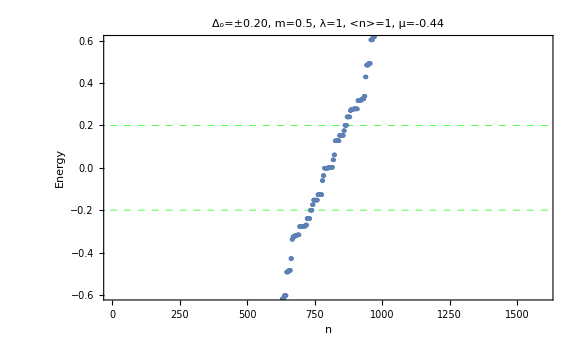

-Graphics-

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{-8.48098, -8.26976, -8.26976, -8.26976, -8.26976, -8.05976, -8.05976, -8.05976, «36», -6.50243, -6.50243, -6.25673, -6.25673, -6.25673, -6.25673, «1550»}, «9»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{-8.48098,-8.26976,-8.26976,-8.26976,-8.26976,-8.05976,-8.05976,-8.05976,«36»,-6.50243,-6.50243,-6.25673,-6.25673,-6.25673,-6.25673,«1550»},«9»]. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

```mathematica
ListPlot[Sort[ES[[1]]],PlotRange->{-0.6,0.6} ,Frame->True,PlotLabel->"Δ_o=±0.20, m=0.5, λ=1, <n>=1, μ=-0.44 ",FrameLabel->{n,Energy},LabelStyle->"DisplayFormula",GridLines->{None,{-0.20,0.20}},GridLinesStyle->Directive[Green, Dashed], Frame->True, FrameStyle->Gray,ImageSize->Large]
```